```mathematica
ClearAll[Evaluate[Context[]<>"*"]]
raw=ToExpression[Import["/home/luca/Documents/ReplyChallenges/STANDARD CODE CHALLENGE 2022 - PANDORA'S ADVENTURES/Q_table"]];
Dimensions@raw
MatrixPlot[raw[[1]]]
MatrixPlot[raw[[2]]]
TURNS=Dimensions[raw][[2]]
```

{2,400,1000}

-Graphics-

-Graphics-

400

```mathematica
MatrixPlot[Table[If[raw[[1,t,s]]>raw[[2,t,s]],1,2],{t,1,TURNS},{s,1,1000}]]
```

-Graphics-

```mathematica
GaussianFilter[raw[[1,All,All]],10];
GaussianFilter[raw[[2,All,All]],10];
ListPointPlot3D[{%%[[;;;;10,;;;;10]],%[[;;;;10,;;;;10]]},PlotRange->All]
ListPointPlot3D[%%%[[;;;;10,;;;;10]]-%%[[;;;;10,;;;;10]],PlotRange->All]
```

-Graphics3D-

-Graphics3D-

```mathematica
ListPlot3D[raw[[1,All,All]],PlotLegends->Automatic,AxesLabel->{"tempo","stamina","policy"}]
```

$Aborted

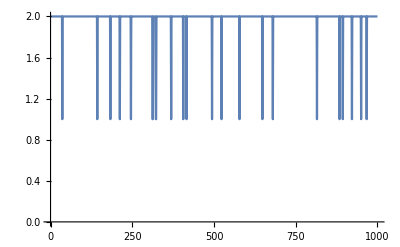

```mathematica
ListLinePlot[Flatten@Table[If[raw[[1,t,s]]>raw[[2,t,s]],1,2],{t,1,1000},{s,{200}}],PlotRange->All]
```